# Introduction

Firms differ in the value that they place on different dimensions of worker input and workers differ in the cost of providing the different dimensions of input. To give an example from academic, some schools care mostly about research, some school care mostly about teaching and some skills have a mixture. Individuals also differ in how costly it is to provide these different

Suppose there are two dimensions to some task, x1 and x2. Firms differ (according to a parameter γ) in how much they value x1 and x2.

```mathematica
y[x1_,x2_]:=γ*x1 + (1-γ)*x2;
```

```mathematica
sol=Solve[y[x1,x2]==1,x2]
```

{{x2→(-1+x1 γ)/(-1+γ)}}

```mathematica
x2Star[x1_]:=x2/.sol[[1]]
```

```mathematica
x2Star[x1]
```

```mathematica
Manipulate[Plot[(-1+x1 γ)/(-1+γ),{x1,0,10},PlotRange->{0,10}],{{γ,0.5},0,1}]
```

Workers differ in their output:

```mathematica
c[x1_,x2_]:=θ*x1 + (1-θ)*x2;
```

```mathematica
Y>0
```

```mathematica
γ>0,γ<1 , θ>0 , θ<1
```

```mathematica
sol=Minimize[{c[x1,x2],y[x1,x2]==Y,x1>=0, x2>=0},{x1,x2}]
```

{Piecewise[{{Y, (θ==0&&γ==0&&Y>0)||(θ==1&&γ==1&&Y>0)}, {-Y/(-1+γ), (θ==0&&γ>1&&Y<0)||(θ==0&&γ<0&&Y>0)}, {Y/γ, (θ==1&&γ>1&&Y>0)||(θ==1&&γ<0&&Y<0)}, {(Y θ)/γ, (θ>1&&γ>θ&&Y>0)||(θ>1&&γ<0&&Y<0)||(0<θ<1&&γ>1&&Y>0)||(0<θ<1&&θ<γ≤1&&Y>0)||(0<θ<1&&γ<0&&Y<0)||(θ<0&&γ>1&&Y>0)||(θ<0&&0<γ≤1&&Y>0)||(θ<0&&γ<θ&&Y<0)}, {(-Y+Y θ)/(-1+γ), (θ>1&&γ==θ&&Y>0)||(θ>1&&γ==θ&&Y<0)||(θ>1&&γ>θ&&Y<0)||(θ>1&&0≤γ<1&&Y>0)||(θ>1&&γ<0&&Y>0)||(0<θ<1&&γ==θ&&Y>0)||(0<θ<1&&γ>1&&Y<0)||(0<θ<1&&0≤γ<θ&&Y>0)||(0<θ<1&&γ<0&&Y>0)||(θ<0&&γ==θ&&Y>0)||(θ<0&&γ==θ&&Y<0)||(θ<0&&γ>1&&Y<0)||(θ<0&&γ<θ&&Y>0)}, {-∞, (θ>1&&1<γ<θ)||(θ<0&&θ<γ<0)||(θ>1&&γ==1&&Y≥0)||(θ<0&&γ==0&&Y≥0)}, {∞, !((θ==0&&γ==0&&Y==0)||(θ==0&&γ>1&&Y==0)||(θ==0&&γ>1&&Y>0)||(θ==0&&0<γ≤1&&Y==0)||(θ==0&&0<γ≤1&&Y>0)||(θ==0&&γ<0&&Y==0)||(θ==0&&γ<0&&Y<0)||(θ==1&&γ==1&&Y==0)||(θ==1&&γ>1&&Y==0)||(θ==1&&γ>1&&Y<0)||(θ==1&&0≤γ<1&&Y==0)||(θ==1&&0≤γ<1&&Y>0)||(θ==1&&γ<0&&Y==0)||(θ==1&&γ<0&&Y>0)||(θ>1&&γ==θ&&Y==0)||(θ>1&&γ>θ&&Y==0)||(θ>1&&0≤γ<1&&Y==0)||(θ>1&&γ<0&&Y==0)||(0<θ<1&&γ==θ&&Y==0)||(0<θ<1&&γ>1&&Y==0)||(0<θ<1&&0≤γ<θ&&Y==0)||(0<θ<1&&θ<γ≤1&&Y==0)||(0<θ<1&&γ<0&&Y==0)||(θ<0&&γ==θ&&Y==0)||(θ<0&&γ>1&&Y==0)||(θ<0&&0<γ≤1&&Y==0)||(θ<0&&γ<θ&&Y==0)||(θ==0&&γ==0&&Y>0)||(θ==1&&γ==1&&Y>0)||(θ==0&&γ>1&&Y<0)||(θ==0&&γ<0&&Y>0)||(θ==1&&γ>1&&Y>0)||(θ==1&&γ<0&&Y<0)||(θ>1&&γ>θ&&Y>0)||(θ>1&&γ<0&&Y<0)||(0<θ<1&&γ>1&&Y>0)||(0<θ<1&&θ<γ≤1&&Y>0)||(0<θ<1&&γ<0&&Y<0)||(θ<0&&γ>1&&Y>0)||(θ<0&&0<γ≤1&&Y>0)||(θ<0&&γ<θ&&Y<0)||(θ>1&&γ==θ&&Y>0)||(θ>1&&γ==θ&&Y<0)||(θ>1&&γ>θ&&Y<0)||(θ>1&&0≤γ<1&&Y>0)||(θ>1&&γ<0&&Y>0)||(0<θ<1&&γ==θ&&Y>0)||(0<θ<1&&γ>1&&Y<0)||(0<θ<1&&0≤γ<θ&&Y>0)||(0<θ<1&&γ<0&&Y>0)||(θ<0&&γ==θ&&Y>0)||(θ<0&&γ==θ&&Y<0)||(θ<0&&γ>1&&Y<0)||(θ<0&&γ<θ&&Y>0)||(θ>1&&1<γ<θ)||(θ<0&&θ<γ<0)||(θ>1&&γ==1&&Y≥0)||(θ<0&&γ==0&&Y≥0))}, {0, True}}],{x1→Piecewise[{{1, (θ==0&&γ==0&&Y==0)||(θ==0&&γ==0&&Y>0)||(θ>1&&γ==θ&&Y==0)||(θ>1&&γ==θ&&Y<0)||(θ<0&&γ==θ&&Y==0)||(θ<0&&γ==θ&&Y>0)}, {Indeterminate, !((θ==0&&γ>1&&Y==0)||(θ==0&&γ>1&&Y<0)||(θ==0&&0<γ≤1&&Y==0)||(θ==0&&γ<0&&Y==0)||(θ==0&&γ<0&&Y>0)||(θ==1&&γ==1&&Y==0)||(θ==1&&γ>1&&Y==0)||(θ==1&&γ>1&&Y<0)||(θ==1&&0≤γ<1&&Y==0)||(θ==1&&0≤γ<1&&Y>0)||(θ==1&&γ<0&&Y==0)||(θ==1&&γ<0&&Y>0)||(θ>1&&γ>θ&&Y==0)||(θ>1&&γ>θ&&Y<0)||(θ>1&&0≤γ<1&&Y==0)||(θ>1&&0≤γ<1&&Y>0)||(θ>1&&γ<0&&Y==0)||(θ>1&&γ<0&&Y>0)||(0<θ<1&&γ==θ&&Y==0)||(0<θ<1&&γ>1&&Y==0)||(0<θ<1&&γ>1&&Y<0)||(0<θ<1&&0≤γ<θ&&Y==0)||(0<θ<1&&0≤γ<θ&&Y>0)||(0<θ<1&&θ<γ≤1&&Y==0)||(0<θ<1&&γ<0&&Y==0)||(0<θ<1&&γ<0&&Y>0)||(θ<0&&γ>1&&Y==0)||(θ<0&&γ>1&&Y<0)||(θ<0&&0<γ≤1&&Y==0)||(θ<0&&γ<θ&&Y==0)||(θ<0&&γ<θ&&Y>0)||(θ==0&&γ==0&&Y==0)||(θ==0&&γ==0&&Y>0)||(θ>1&&γ==θ&&Y==0)||(θ>1&&γ==θ&&Y<0)||(θ<0&&γ==θ&&Y==0)||(θ<0&&γ==θ&&Y>0)||(θ==1&&γ==1&&Y>0)||(θ==1&&γ>1&&Y>0)||(θ==1&&γ<0&&Y<0)||(θ==0&&γ>1&&Y>0)||(θ==0&&0<γ≤1&&Y>0)||(θ==0&&γ<0&&Y<0)||(0<θ<1&&γ==θ&&Y>0)||(θ>1&&γ>θ&&Y>0)||(θ>1&&γ<0&&Y<0)||(0<θ<1&&γ>1&&Y>0)||(0<θ<1&&θ<γ≤1&&Y>0)||(0<θ<1&&γ<0&&Y<0)||(θ<0&&γ>1&&Y>0)||(θ<0&&0<γ≤1&&Y>0)||(θ<0&&γ<θ&&Y<0)||(θ>1&&γ==θ&&Y>0)||(θ<0&&γ==θ&&Y<0))}, {Y, θ==1&&γ==1&&Y>0}, {Y/γ, (θ==1&&γ>1&&Y>0)||(θ==1&&γ<0&&Y<0)||(θ==0&&γ>1&&Y>0)||(θ==0&&0<γ≤1&&Y>0)||(θ==0&&γ<0&&Y<0)||(θ>1&&γ>θ&&Y>0)||(θ>1&&γ<0&&Y<0)||(0<θ<1&&γ>1&&Y>0)||(0<θ<1&&θ<γ≤1&&Y>0)||(0<θ<1&&γ<0&&Y<0)||(θ<0&&γ>1&&Y>0)||(θ<0&&0<γ≤1&&Y>0)||(θ<0&&γ<θ&&Y<0)}, {(-Y+Y θ)/(2 (-1+γ) θ), 0<θ<1&&γ==θ&&Y>0}, {(-Y-θ+Y θ+γ θ)/((-1+γ) θ), (θ>1&&γ==θ&&Y>0)||(θ<0&&γ==θ&&Y<0)}, {0, True}}],x2→Piecewise[{{1, (θ==1&&γ==1&&Y==0)||(θ==1&&γ==1&&Y>0)}, {Indeterminate, !((θ==0&&γ==0&&Y==0)||(θ==0&&γ>1&&Y==0)||(θ==0&&γ>1&&Y>0)||(θ==0&&0<γ≤1&&Y==0)||(θ==0&&0<γ≤1&&Y>0)||(θ==0&&γ<0&&Y==0)||(θ==0&&γ<0&&Y<0)||(θ==1&&γ>1&&Y==0)||(θ==1&&γ>1&&Y>0)||(θ==1&&0≤γ<1&&Y==0)||(θ==1&&γ<0&&Y==0)||(θ==1&&γ<0&&Y<0)||(θ>1&&γ>θ&&Y==0)||(θ>1&&γ>θ&&Y>0)||(θ>1&&0≤γ<1&&Y==0)||(θ>1&&γ<0&&Y==0)||(θ>1&&γ<0&&Y<0)||(0<θ<1&&γ==θ&&Y==0)||(0<θ<1&&γ>1&&Y==0)||(0<θ<1&&γ>1&&Y>0)||(0<θ<1&&0≤γ<θ&&Y==0)||(0<θ<1&&θ<γ≤1&&Y==0)||(0<θ<1&&θ<γ≤1&&Y>0)||(0<θ<1&&γ<0&&Y==0)||(0<θ<1&&γ<0&&Y<0)||(θ<0&&γ>1&&Y==0)||(θ<0&&γ>1&&Y>0)||(θ<0&&0<γ≤1&&Y==0)||(θ<0&&0<γ≤1&&Y>0)||(θ<0&&γ<θ&&Y==0)||(θ<0&&γ<θ&&Y<0)||(θ==1&&γ==1&&Y==0)||(θ==1&&γ==1&&Y>0)||(θ==0&&γ==0&&Y>0)||(θ==0&&γ>1&&Y<0)||(θ==0&&γ<0&&Y>0)||(θ==1&&γ>1&&Y<0)||(θ==1&&0≤γ<1&&Y>0)||(θ==1&&γ<0&&Y>0)||(θ>1&&γ==θ&&Y==0)||(θ<0&&γ==θ&&Y==0)||(θ>1&&γ>θ&&Y<0)||(θ>1&&0≤γ<1&&Y>0)||(θ>1&&γ<0&&Y>0)||(0<θ<1&&γ>1&&Y<0)||(0<θ<1&&0≤γ<θ&&Y>0)||(0<θ<1&&γ<0&&Y>0)||(θ<0&&γ>1&&Y<0)||(θ<0&&γ<θ&&Y>0)||(0<θ<1&&γ==θ&&Y>0)||(θ>1&&γ==θ&&Y<0)||(θ<0&&γ==θ&&Y>0)||(θ>1&&γ==θ&&Y>0)||(θ<0&&γ==θ&&Y<0))}, {Y, θ==0&&γ==0&&Y>0}, {-Y/(-1+γ), (θ==0&&γ>1&&Y<0)||(θ==0&&γ<0&&Y>0)||(θ==1&&γ>1&&Y<0)||(θ==1&&0≤γ<1&&Y>0)||(θ==1&&γ<0&&Y>0)||(θ>1&&γ>θ&&Y<0)||(θ>1&&0≤γ<1&&Y>0)||(θ>1&&γ<0&&Y>0)||(0<θ<1&&γ>1&&Y<0)||(0<θ<1&&0≤γ<θ&&Y>0)||(0<θ<1&&γ<0&&Y>0)||(θ<0&&γ>1&&Y<0)||(θ<0&&γ<θ&&Y>0)}, {-Y/(2 (-1+γ)), 0<θ<1&&γ==θ&&Y>0}, {θ/(-1+θ), (θ>1&&γ==θ&&Y==0)||(θ<0&&γ==θ&&Y==0)||(θ>1&&γ==θ&&Y>0)||(θ<0&&γ==θ&&Y<0)}, {(Y-θ-Y θ+γ θ)/((-1+γ) (-1+θ)), (θ>1&&γ==θ&&Y<0)||(θ<0&&γ==θ&&Y>0)}, {0, True}}]}}

```mathematica
Simplify[sol,θ>0 && θ<1 && Y > 0 && γ>0 && γ<1]//FullSimplify
```

{Piecewise[{{(Y θ)/γ, γ>θ}, {(Y (-1+θ))/(-1+γ), True}}],{x1→Piecewise[{{Y/γ, γ>θ}, {Y/(2 θ), γ==θ}, {0, True}}],x2→Piecewise[{{-Y/(-1+γ), γ<θ}, {Y/(2-2 γ), γ==θ}, {0, True}}]}}

```mathematica
X[γ_,θ_,Y_]:=If[γ > θ,{Y/γ,0}, {0,Y/(1-γ)}]
```

```mathematica
X[2,1,1]
```

{1/2,0}

```mathematica
Y[x1_,x2_,γ_]:=γ*x1 + (1-γ)*x2;
```

```mathematica
Manipulate[RegionPlot[{Y[x1,x2,g1]>1,Y[x1,x2,g2]>1},{x1,0,2},{x2,0,2}],{{g1,0.5},0,1},{{g2,0.5},0,1}]
```

If we assume that in a competetive equilibrium, firms of different types earn equal profits.

```mathematica
Solve[Y[x1,x2,g1]==Y[x1,x2,g2],{x1,x2}]
```

{{x2→x1}}

It doesn't matter what the prior distribution of types might be: the worker still chooses the safe, average level of output.

Workers have to decide: produce at the corner solution or produce at the safe level.

```mathematica
c[w/2,w/2]//FullSimplify
```

w/2

```mathematica
c[w/γ,0]//FullSimplify
```

(w θ)/γ

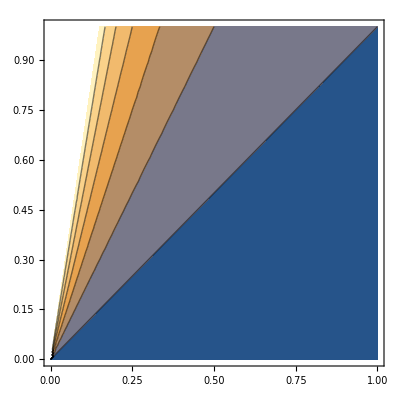

```mathematica
ContourPlot[θ/γ,{γ,0,1},{θ,0,1}]
```

```mathematica
c[0,w/(1-γ)]
```

(w (1-θ))/(1-γ)